```mathematica
<<Wolfram`QuantumFramework`
```

### 12.1 [BSc] How do I build a Werner state and locate its entanglement threshold?

A Werner state is a singlet diluted by white noise, and what picks the family out is a symmetry: these are the two-qubit states left unchanged when the same unitary acts on both qubits. That invariance leaves exactly one free parameter, so every statement below depends on which parameter is meant, and the convention has to be fixed before a threshold can be quoted. Take

ρ_W(λ)=λ |Ψ^-⟩⟨Ψ^-|+(1-λ)I/4

so λ is the weight on the singlet and 1−λ the weight on the uniform mixture. Read it as a mixing probability where λ runs over 0≤λ≤1, from white noise to a pure singlet, but positivity of ρ_W is the only real constraint which the spectrum below settles. As λ falls the noise washes the entanglement out, and the value of λ where that happens is the threshold

WL:

Build the Werner state family for two qubits using the standard definition with the λ convention:

```mathematica
MatrixForm[werner=With[{singlet=Normalize@Flatten[KroneckerProduct[{1,0},{0,1}]-KroneckerProduct[{0,1},{1,0}]]},λ KroneckerProduct[singlet,singlet]+(1-λ) IdentityMatrix[4]/4]]
```

((1-λ)/4 | 0 | 0 | 0
0 | (1-λ)/4+λ/2 | -λ/2 | 0
0 | -λ/2 | (1-λ)/4+λ/2 | 0
0 | 0 | 0 | (1-λ)/4)

Verify the symmetry:

```mathematica
With[{u={{Cos[θ/2] Exp[ⅈ ϕ],Sin[θ/2] Exp[ⅈ ψ]},{-Sin[θ/2] Exp[-ⅈ ψ],Cos[θ/2] Exp[-ⅈ ϕ]}}},Simplify[{ConjugateTranspose[u].u==IdentityMatrix[2],KroneckerProduct[u,u].werner.ConjugateTranspose[KroneckerProduct[u,u]]==werner},{θ,ϕ,ψ}∈Reals]]
```

{True,True}

Calculate the spectrum:

```mathematica
{Simplify@Eigenvalues[werner],Reduce[And@@Thread[Eigenvalues[werner]>=0],λ,Reals]}
```

{{(1-λ)/4,(1-λ)/4,(1-λ)/4,1/4 (1+3 λ)},-1/3≤λ≤1}

Transposing the second qubit alone moves one eigenvalue against the other three:

```mathematica
Simplify@Eigenvalues@ArrayReshape[Transpose[ArrayReshape[werner,{2,2,2,2}],{1,4,3,2}],{4,4}]
```

{1/4 (1-3 λ),(1+λ)/4,(1+λ)/4,(1+λ)/4}

The threshold is where that eigenvalue turns negative:

```mathematica
Reduce[Min[Eigenvalues@ArrayReshape[Transpose[ArrayReshape[werner,{2,2,2,2}],{1,4,3,2}],{4,4}]]<0&&-1/3<=λ<=1,λ,Reals]
```

1/3<λ≤1

The concurrence is an exact measure rather than a criterion, so it locates the same point and also says how much entanglement survives above it:

```mathematica
With[{y=KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]},Simplify[Max[0,2 Max[#]-Total[#]]&@Sqrt@Simplify@Eigenvalues[werner.y.Conjugate[werner].y],-1/3<=λ<=1]]
```

Piecewise[{{1/2 (-1+3 λ), 3 λ>1}, {0, True}}]

QF:

QF uses the following convention
ρ_W^QF(p) = (1-p)|ψ^-⟩⟨ψ^-|+p/3(I-|ψ^-⟩⟨ψ^-|)      with   0≤p≤1

Define a Werner state:

```mathematica
TraditionalForm[wernerQF = QuantumState["Werner"[p,2]]]
```

p/3 0000+1/6 (3-2 p)0101+1/6 (4 p-3)0110+1/6 (4 p-3)1001+1/6 (3-2 p)1010+p/3 1111

Verify the definition of QF Werner state:

```mathematica
Simplify[With[{s=QuantumState["PsiMinus"]["MatrixState"]},(1-p)s+p/3(QuantumState[IdentityMatrix[4],{2,2}]-s)]]
```

p/3 0000+1/6 (3-2 p)0101+1/6 (4 p-3)0110+1/6 (4 p-3)1001+1/6 (3-2 p)1010+p/3 1111

```mathematica
wernerQF==%
```

True

Its spectrum names the parameter, p is the weight spread over the triplet, and 1−p is what stays on the singlet:

```mathematica
Simplify@wernerQF["Eigenvalues"]
```

{1-p,p/3,p/3,p/3}

One family in two coordinates, we can solve for the mapping that relates the two conventions:

```mathematica
Solve[Normal[QuantumState["Werner"[p,2]]["DensityMatrix"]]==werner,λ]//Simplify
```

{{λ→1-(4 p)/3}}

We can find the entanglement threshold with the “Concurrence” metric:

```mathematica
threshold =Simplify[QuantumEntanglementMonotone[wernerQF,"Concurrence"],0<=p<=1]
```

Piecewise[{{1-2 p, 2 p<1}, {0, True}}]

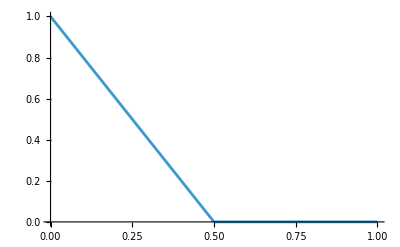

```mathematica
Plot[threshold,{p,0,1}]
```

The two thresholds λ=1/3and p=1/2  are the same physical point, since the conversion carries one inequality onto the other a singlet tolerates white noise up to two thirds of the total weight, and no further.

### 12.2 [BSc] How do I purify a mixed state and recover it by partial trace?

A mixed state is what a pure state looks like when part of the world is out of view, and purification makes that literal: adjoin an ancilla B and produce a pure |ψ⟩ on A B whose reduced state on A is the ρ we started with. Writing ρ=∑_i p_i|e_i⟩⟨e_i| the vector |ψ⟩= ∑_i √p_i|e_i⟩_A⊗ |i⟩_B is pure and tracing out B against the orthonormal 
∣i⟩_B  returns each and nothing else, so the ancilla needs only as many dimensions as ρ has nonzero eigenvalues. Take the generic mixed qubit in Bloch form,  the unit vector at angles (θ,φ) its eigenvalues are (1±r)/2, so one ancilla qubit is enough.

WL:

The state with the Bloch vector split into its length and its direction:

```mathematica
rho=With[{nvec={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}},1/2 (IdentityMatrix[2]+r nvec.PauliMatrix[{1,2,3}])]
```

{{1/2 (1+r Cos[θ]),1/2 r (Cos[ϕ] Sin[θ]-ⅈ Sin[θ] Sin[ϕ])},{1/2 r (Cos[ϕ] Sin[θ]+ⅈ Sin[θ] Sin[ϕ]),1/2 (1-r Cos[θ])}}

Its eigenvectors are the spin-up and spin-down states along  n̂, orthonormal, and weighting their projectors by (1±r)/2 rebuilds ρ:

```mathematica
{up,down}={{Cos[θ/2],Exp[ⅈ ϕ] Sin[θ/2]},{-Exp[-ⅈ ϕ] Sin[θ/2],Cos[θ/2]}};Simplify[{Conjugate[up].up,Conjugate[down].down,Conjugate[up].down,rho==1/2 (1+r) KroneckerProduct[up,Conjugate[up]]+1/2 (1-r) KroneckerProduct[down,Conjugate[down]]},{θ,ϕ}∈Reals]
```

{1,1,0,True}

Pairing each eigenvector with its own ancilla ket, amplitudes the square roots of the eigenvalues, gives the purification:

```mathematica
psi=Simplify[√((1+r)/2) Flatten[KroneckerProduct[up,{1,0}]]+√((1-r)/2) Flatten[KroneckerProduct[down,{0,1}]],{θ,ϕ}∈Reals]
```

{(√(1+r) Cos[θ/2])/(√2),-(√(1-r) ⅇ^(-ⅈ ϕ) Sin[θ/2])/(√2),(√(1+r) ⅇ^(ⅈ ϕ) Sin[θ/2])/(√2),(√(1-r) Cos[θ/2])/(√2)}

It is a unit vector, and contracting the ancilla index against itself returns the original state exactly:

```mathematica
Simplify[{Conjugate[psi].psi,ArrayReshape[TensorContract[ArrayReshape[KroneckerProduct[psi,Conjugate[psi]],{2,2,2,2}],{{2,4}}],{2,2}]==rho},0≤r≤1&&{θ,ϕ}∈Reals]
```

{1,True}

Tracing the other way leaves the ancilla in a state carrying the same spectrum, so whatever mixedness ρ has is shared symmetrically across the cut:

```mathematica
Simplify[Eigenvalues@Simplify[ArrayReshape[TensorContract[ArrayReshape[KroneckerProduct[psi,Conjugate[psi]],{2,2,2,2}],{{1,3}}],{2,2}],Element[{θ,ϕ},Reals]],0<=r<=1]
```

{(1-r)/2,(1+r)/2}

The choice of ancilla basis was free, so a unitary acting on B alone sends one purification to another with the same reduced state:

```mathematica
v={{Cos[a/2] Exp[I b],Sin[a/2] Exp[I c]},{-Sin[a/2] Exp[-I c],Cos[a/2] Exp[-I b]}};Simplify[{ConjugateTranspose[v].v==IdentityMatrix[2],ComplexExpand[ArrayReshape[TensorContract[ArrayReshape[KroneckerProduct[#,Conjugate[#]]&@(KroneckerProduct[IdentityMatrix[2],v].psi),{2,2,2,2}],{{2,4}}],{2,2}]]==rho},0<=r<=1&&Element[{θ,ϕ,a,b,c},Reals]]
```

{True,True}

QF:

```mathematica
TraditionalForm[qs=QuantumState["BlochVector"[r {Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}]]//FullSimplify]
```

1/2 (r cos(θ)+1)00+1/2 ⅇ^(-ⅈ ϕ) r sin(θ)01+1/2 ⅇ^(ⅈ ϕ) r sin(θ)10+1/2 (1-r cos(θ))11

Compute the eigenvalues:

```mathematica
qs["Eigenvalues"]
```

{(1-r)/2,(1+r)/2}

Use the “Purify” property of the framework:

```mathematica
TraditionalForm[purified =FullSimplify[qs["Purify"],0<r<1]]
```

((√(r+1)-√(1-r)) cos(θ)+√(1-r)+√(r+1))/(2 √2)00+(ⅇ^(-ⅈ ϕ) (√(r+1)-√(1-r)) sin(θ))/(2 √2)01-(ⅇ^(ⅈ ϕ) (√(1-r)-√(r+1)) sin(θ))/(2 √2)10+((√(1-r)-√(r+1)) cos(θ)+√(1-r)+√(r+1))/(2 √2)11

Check dimensions:

```mathematica
{qs["Dimensions"],purified["Dimensions"],purified["PureStateQ"]}
```

{{2},{2,2},True}

Verify the partial trace of B returns the original mixed state:

```mathematica
FullSimplify[QuantumPartialTrace[purified,{2}],0<r<1&&Element[{ϕ,θ},Reals]]==qs
```

True

#### 12.3 [MSc] How do I show that different ensembles can give the same density matrix (the ensemble ambiguity / unitary freedom)?

A density matrix records and forgets the list that built it, so the preparer’s ensemble is not recoverable from the state. Absorbing each weight into its vector, , turns the sum into ρ, and in that form the freedom is a single line of algebra.

The Hughston-Jozsa-Wootters theorem says the converse too: every ensemble for ρ arises this way, from the eigen-ensemble, with U an isometry rather than a square unitary when the new list is longer. Since U need not be square, neither the weights, nor the states, nor even how many of them there are is fixed by 
ρ. Take the generic mixed qubit ρ=1/2(I+r n̂·σ⃗) again.

WL:

The state, and the ensemble its own spectrum provides, weights folded into the vectors:

```mathematica
rho=With[{nvec={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}},1/2 (IdentityMatrix[2]+r nvec.PauliMatrix[{1,2,3}])]
ens={Sqrt[(1+r)/2] {Cos[θ/2],Exp[I ϕ] Sin[θ/2]},Sqrt[(1-r)/2] {-Exp[-I ϕ] Sin[θ/2],Cos[θ/2]}}
```

{{1/2 (1+r Cos[θ]),1/2 r (Cos[ϕ] Sin[θ]-ⅈ Sin[θ] Sin[ϕ])},{1/2 r (Cos[ϕ] Sin[θ]+ⅈ Sin[θ] Sin[ϕ]),1/2 (1-r Cos[θ])}}

{{(√(1+r) Cos[θ/2])/(√2),(√(1+r) ⅇ^(ⅈ ϕ) Sin[θ/2])/(√2)},{-(√(1-r) ⅇ^(-ⅈ ϕ) Sin[θ/2])/(√2),(√(1-r) Cos[θ/2])/(√2)}}

Its members square-sum to ρ, and their norms are the eigenvalues, so this is the orthogonal ensemble the spectral decomposition names:

```mathematica
Simplify[{Total[KroneckerProduct[#,Conjugate[#]]&/@ens]==rho,Conjugate[#].#&/@ens},0<=r<=1&&Element[{θ,ϕ},Reals]]
```

{True,{(1+r)/2,(1-r)/2}}

Mixing the two members with a generic SU(2) matrix produces another ensemble for the same ρ, with its own weights and its own mutual overlap:

```mathematica
u={{Cos[a/2] Exp[I b],Sin[a/2] Exp[I c]},{-Sin[a/2] Exp[-I c],Cos[a/2] Exp[-I b]}};Simplify[ComplexExpand[{Total[KroneckerProduct[#,Conjugate[#]]&/@(u.ens)]==rho,Conjugate[#].#&/@(u.ens),Conjugate[First[u.ens]].Last[u.ens]}],0<=r<=1&&Element[{θ,ϕ,a,b,c},Reals]]
```

{True,{1/2 (1+r Cos[a]),1/2 (1-r Cos[a])},-1/2 r Sin[a] (Cos[b+c]-ⅈ Sin[b+c])}

The isometry need not be square, so the member count is not fixed either, four columns of length two, orthonormal as columns, turn two states into four:

```mathematica
v=1/2 {{1,1},{1,-1},{1,I},{1,-I}};Simplify[ComplexExpand[{ConjugateTranspose[v].v==IdentityMatrix[2],Total[KroneckerProduct[#,Conjugate[#]]&/@(v.ens)]==rho,Conjugate[#].#&/@(v.ens)}],0<=r<=1&&Element[{θ,ϕ},Reals]]
```

{True,True,{1/4,1/4,1/4,1/4}}

QF:

Stacking the ensemble members against orthonormal ancilla kets is exactly the purification of Part 12.2, so an observer holding the ancilla can choose which ensemble the system is in, by choosing what to measure:

```mathematica
qpsi=QuantumState[Flatten@ens]["Reverse"]
```

(√(r+1) cos(θ/2))/(√2)00-(ⅇ^(-ⅈ ϕ) √(1-r) sin(θ/2))/(√2)01+(ⅇ^(ⅈ ϕ) √(r+1) sin(θ/2))/(√2)10+(√(1-r) cos(θ/2))/(√2)11

Measuring the ancilla in the computational basis returns the eigen-ensemble weights; measuring it along X returns an unbiased pair instead:

```mathematica
Simplify[{Values@QuantumMeasurementOperator[{2}][qpsi]["Probabilities"],Values@QuantumMeasurementOperator[QuantumOperator["X",{2}]][qpsi]["Probabilities"]},0<=r<=1&&Element[{θ,ϕ},Reals]]
```

{{(1+r)/2,(1-r)/2},{1/2,1/2}}

Either way the conditional states of the system, weighted by the outcome probabilities they come with, rebuild the same ρ, which is what stops the choice from being detectable on the system alone:

```mathematica
Simplify[(Total[(Normal[QuantumPartialTrace[#1,{2}]["DensityMatrix"]]&)/@Values[#1["StateAssociation"]]]==rho&)/@{QuantumMeasurementOperator[{2}][qpsi],QuantumMeasurementOperator[QuantumOperator["X",{2}]][qpsi]},0≤r≤1&&{θ,ϕ}∈Reals]
```

{True,True}

### 12.4 [BSc] How do I build the Gibbs (thermal) state ρ = ⅇ^(-β H/Z), Z=Tr ⅇ^(-β H), and compute thermal averages ⟨A⟩=Tr[Aρ]?

WL:

The Hamiltonian, written in the same Bloch form the states of 12.2 and 12.3 use:

```mathematica
ham=With[{nvec={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}},w/2 nvec.PauliMatrix[{1,2,3}]]
```

{{1/2 w Cos[θ],1/2 w (Cos[ϕ] Sin[θ]-ⅈ Sin[θ] Sin[ϕ])},{1/2 w (Cos[ϕ] Sin[θ]+ⅈ Sin[θ] Sin[ϕ]),-1/2 w Cos[θ]}}

Its two levels sit at  ±ω/2, and the partition function is the trace of the matrix exponential:

```mathematica
{Simplify[Eigenvalues[ham],w>0&&{θ,ϕ}∈Reals],
Simplify[ExpToTrig[Simplify[Tr[MatrixExp[-b ham]],w>0&&b>0&&{θ,ϕ}∈Reals]]]}
```

{{-w/2,w/2},2 Cosh[(b w)/2]}

Dividing the exponential by that trace gives the state, and it is again a Bloch vector: pointing along -n̂ , of length set by the temperature alone:

```mathematica
gibbs=Simplify[MatrixExp[-b ham]/Tr@MatrixExp[-b ham],w>0&&b>0&&Element[{θ,ϕ},Reals]];Simplify[gibbs==With[{nvec={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}},1/2 (IdentityMatrix[2]-Tanh[b w/2] nvec.PauliMatrix[{1,2,3}])],w>0&&b>0&&Element[{θ,ϕ},Reals]]
```

True

A thermal average is a trace against that state. Doing it for Ĥ  itself, and differentiating  logZ, are two routes to the same number:

```mathematica
Simplify@ExpToTrig@Simplify[{Tr[ham.gibbs],-D[Log[Tr@MatrixExp[-b ham]],b]},w>0&&b>0&&Element[{θ,ϕ},Reals]]
```

{-1/2 w Tanh[(b w)/2],-1/2 w Tanh[(b w)/2]}

The entropy comes from the same spectrum, and the thermodynamic identity relating it to the energy and the free energy is an algebraic consequence rather than a further assumption:

```mathematica
FullSimplify[{-Total[# Log[#]&/@Eigenvalues[gibbs]]==Log[2 Cosh[b w/2]]-(b w/2) Tanh[b w/2],-Total[# Log[#]&/@Eigenvalues[gibbs]]==b (Tr[ham.gibbs]+Log[Tr@MatrixExp[-b ham]]/b)},w>0&&b>0&&Element[{θ,ϕ},Reals]]
```

{True,True}

Both temperature limits are limits of the single number  tanh(βω/2), and the cold end lands on the eigen-projector for the lower level:

```mathematica
With[{nvec={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}},{Limit[Tanh[b w/2],b->0],Limit[Tanh[b w/2],b->Infinity,Assumptions->w>0],Simplify[ham.(1/2 (IdentityMatrix[2]-nvec.PauliMatrix[{1,2,3}]))==-(w/2) (1/2 (IdentityMatrix[2]-nvec.PauliMatrix[{1,2,3}])),w>0&&Element[{θ,ϕ},Reals]]}]
```

{0,1,True}

QF:

Define the Hamiltonian:

```mathematica
hq=Dot[w/2{Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]},QuantumOperator/@{"X","Y","Z"}]
```

1/2 w Cos[θ]00+(1/2 w Cos[ϕ] Sin[θ]-1/2 ⅈ w Sin[θ] Sin[ϕ])01+(1/2 w Cos[ϕ] Sin[θ]+1/2 ⅈ w Sin[θ] Sin[ϕ])10-1/2 w Cos[θ]11

The Gibbs state is its matrix handed to QuantumState and normalized. The state reports its own Bloch vector, which is where the temperature shows up:

```mathematica
gq=QuantumState[MatrixExp[-b hq]["Matrix"],2]["Normalized"];Simplify@ExpToTrig@Simplify[gq["BlochVector"],w>0&&b>0&&Element[{θ,ϕ},Reals]]
```

{-Cos[ϕ] Sin[θ] Tanh[(b w)/2],-Sin[θ] Sin[ϕ] Tanh[(b w)/2],-Cos[θ] Tanh[(b w)/2]}

The mean energy is the trace of the operator against the state:

```mathematica
Simplify@ExpToTrig@Simplify[Tr[hq@gq["Operator"]],w>0&&b>0&&Element[{θ,ϕ},Reals]]
```

-1/2 w Tanh[(b w)/2]

“VonNeumannEntropy” is a Quantity carrying its unit, and it counts in bits, so it is the WL entropy divided by log2:

```mathematica
gq["VonNeumannEntropy"]
```

-(Log[1/(1+ⅇ^(b w))]+ⅇ^(b w) Log[ⅇ^(b w)/(1+ⅇ^(b w))])/(Log[2]+ⅇ^(b w) Log[2]) b

```mathematica
Simplify[QuantityMagnitude[%]+Total[# Log[#]&/@Eigenvalues[gibbs]]/Log[2]]
```

0

The two-level Gibbs state is 1/2(I-tanh(β ω/2)n̂· σ⃗), verified as an identity for every axis and temperature, so the whole thermal family is the segment of the Bloch line along n̂ of length tanh(βω/2). The minus sign is Boltzmann weighting,  population accumulates on the lower level, opposite the field. The partition function is 
Z=2cosh(βω/2), and the mean energy  ⟨H⟩= -ω/2 tanh(βω/2) arrives identically from the trace Tr[Hρ] and from −∂_β  logZ

### 12.5 [BSc] How do I compare two states by trace distance and (pure-state) fidelity?

WL:

Two generic mixed qubits, each carrying its own Bloch vector:

```mathematica
{rho1,rho2}=1/2 (IdentityMatrix[2]+#.PauliMatrix[{1,2,3}])&/@{{x,y,z},{u,v,w}}
```

{{{(1+z)/2,1/2 (x-ⅈ y)},{1/2 (x+ⅈ y),(1-z)/2}},{{(1+w)/2,1/2 (u-ⅈ v)},{1/2 (u+ⅈ v),(1-w)/2}}}

The difference of two states is traceless, so its two eigenvalues are equal and opposite and the trace norm collapses to the length of the Bloch separation:

```mathematica
Simplify[Total[Abs[Eigenvalues[rho1-rho2]]]/2==EuclideanDistance[{x,y,z},{u,v,w}]/2,Element[{x,y,z,u,v,w},Reals]]
```

True

Now to consider pure-state fidelity, we drop to two generic pure qubits. Their squared overlap is fixed by the angle between their Bloch vectors alone, the phases cancelling:

```mathematica
FullSimplify[ComplexExpand[Abs[Conjugate[{Cos[t/2],Exp[ⅈ p] Sin[t/2]}].{Cos[a/2],Exp[ⅈ b] Sin[a/2]}]^2]==1/2 (1+{Sin[t] Cos[p],Sin[t] Sin[p],Cos[t]}.{Sin[a] Cos[b],Sin[a] Sin[b],Cos[a]}),{t,p,a,b}∈Reals]
```

True

On the Bloch sphere the two measures are then locked together, since a chord and the angle it subtends carry the same information:

```mathematica
Simplify[1/2 EuclideanDistance[{Sin[t] Cos[p],Sin[t] Sin[p],Cos[t]},{Sin[a] Cos[b],Sin[a] Sin[b],Cos[a]}]==√(1-1/2 (1+{Sin[t] Cos[p],Sin[t] Sin[p],Cos[t]}.{Sin[a] Cos[b],Sin[a] Sin[b],Cos[a]})),{t,p,a,b}∈Reals]
```

True

QF:

QuantumDistance takes the measure as a third argument, where the trace distance is named “Trace” and “Bloch” is the Bloch-vector separation. For a qubit those are the same number:

```mathematica
{q1,q2}=(QuantumState["BlochVector"[#1]]&)/@{{x,y,z},{u,v,w}};Simplify[{QuantumDistance[q1,q2,"Trace"]==QuantumDistance[q1,q2,"Bloch"],QuantumDistance[q1,q2,"Trace"]==1/2 EuclideanDistance[{x,y,z},{u,v,w}]},{x,y,z,u,v,w}∈Reals]
```

{True,True}

For two pure qubits a common unitary rotates one to the north pole and the other into the  x-z plane, so a single angle θ between the Bloch vectors carries everything. Three numbers, three different conventions:

```mathematica
{p1,p2}=QuantumState/@{{1,0},{Cos[t/2],Sin[t/2]}};FullSimplify[{QuantumSimilarity[p1,p2,"Fidelity"],QuantumDistance[p1,p2],QuantumDistance[p1,p2,"Trace"]},0<=t<=Pi]
```

{Cos[t/2],2 Sin[t/4]^2,Sin[t/2]}

The first is √F and the second is a distance built from it, not the fidelity, so the two are complementary rather than equal, and only the third is the D defined above:

```mathematica
FullSimplify[{QuantumDistance[p1,p2]+QuantumSimilarity[p1,p2,"Fidelity"]==1,QuantumDistance[p1,p2,"Trace"]==Sqrt[1-QuantumSimilarity[p1,p2,"Fidelity"]^2]},0<=t<=Pi]
```

{True,True}

### 12.6 [MSc] How do I compute the Uhlmann fidelity F(ρ, σ) = (Tr √(√ρ σ √ρ))^2 between two mixed states?

Two generic mixed qubits again, each with its own Bloch vector:

```mathematica
{rho1,rho2}=1/2 (IdentityMatrix[2]+#.PauliMatrix[{1,2,3}])&/@{{x,y,z},{u,v,w}}
```

{{{(1+z)/2,1/2 (x-ⅈ y)},{1/2 (x+ⅈ y),(1-z)/2}},{{(1+w)/2,1/2 (u-ⅈ v)},{1/2 (u+ⅈ v),(1-w)/2}}}

The two eigenvalues of the product are never needed individually, only their sum and their product enter, and those are a trace and a pair of determinants:

```mathematica
Simplify[{Total[Eigenvalues[rho1.rho2]]==Tr[rho1.rho2],Times@@Eigenvalues[rho1.rho2]==Det[rho1] Det[rho2]},Element[{x,y,z,u,v,w},Reals]]
```

{True,True}

Squaring a sum of two square roots returns the sum plus twice the root of the product, which is the step that turns the definition into a formula:

```mathematica
Simplify[Tr[rho1.rho2]+2 Sqrt[Det[rho1] Det[rho2]]==(1+{x,y,z}.{u,v,w}+Sqrt[(1-{x,y,z}.{x,y,z}) (1-{u,v,w}.{u,v,w})])/2,Element[{x,y,z,u,v,w},Reals]]
```

True

So F=Tr[ρ σ]+2 √(det ρ det σ) , and in Bloch coordinates every piece is elementary: the trace is an inner product of Bloch vectors and each determinant measures how far its state sits from the surface. And can be expressed as F=1/2(1+OverVector[r_1]·(r⃗)_2+√((1-|r_1|^2)(1-|r_2|)^2))

```mathematica
{sig1,sig2}={1/2 (IdentityMatrix[2]+{0,0,a}.PauliMatrix[{1,2,3}]),1/2 (IdentityMatrix[2]+{b Sin[c],0,b Cos[c]}.PauliMatrix[{1,2,3}])};FullSimplify[{Tr[MatrixPower[MatrixPower[sig1,1/2].sig2.MatrixPower[sig1,1/2],1/2]]^2==1/2 (1+a b Cos[c]+√((1-a^2) (1-b^2))),Tr[MatrixPower[MatrixPower[sig1,1/2].sig2.MatrixPower[sig1,1/2],1/2]]==Tr[MatrixPower[sig1.sig2,1/2]]},0≤a≤1&&0≤b≤1&&0≤c≤π]
```

{True,True}

QF:

Define symbolic states from Bloch vectors:

```mathematica
TraditionalForm[{qs1,qs2}=QuantumState["BlochVector"[#]]&/@{{0,0,a},{b Sin[c],0,b Cos[c]}}]
```

{(a/2+1/2)00+(1/2-a/2)11,(1/2 b cos(c)+1/2)00+1/2 b sin(c)01+1/2 b sin(c)10+(1/2-1/2 b cos(c))11}

QuantumSimilarity with the “Fidelity” measure computes √F and not F  so squaring it is what matches the definition above:

```mathematica
FullSimplify[QuantumSimilarity[qs1,qs2,"Fidelity"]^2,0≤a≤1&&0≤b≤1&&0≤c≤π]
```

1/2 (1+√((-1+a^2) (-1+b^2))+a b Cos[c])

Also this property F(ρ, σ)= F(σ, ρ) has to hold:

```mathematica
QuantumSimilarity[qs1,qs2,"Fidelity"]==QuantumSimilarity[qs2,qs1,"Fidelity"]
```

True

Check against the vector definition:

```mathematica
Simplify[With[{v1={0,0,a},v2={b Sin[c],0,b Cos[c]}},1/2 (1+v1.v2+√((1-Norm[v1]^2)(1-Norm[v2]^2)))],0<=a<=1&&0<=b<=1&&0<=c<=Pi]
```

1/2 (1+√((-1+a^2) (-1+b^2))+a b Cos[c])

### 12.7 [MSc] How do I find the optimal state-discrimination measurement and the Helstrom error probability P_err=1/2(1-||p_1 ρ_1-p_2 ρ_2(||)_1)

One of two known states arrives, ρ_1with prior p and ρ_2 with prior 1−p, and a single measurement must name which. The apparatus is a two-outcome POVM 
{E_1,E_2}, outcome E_2 meaning “it was ρ_2”, so P_err=ρ Tr[ρ_1 E_2]+(1-p)Tr[ρ_2 E_1]=(1-p)+Tr[Λ E_2], Λ=pρ_1-(1-p)ρ_2. Only  Tr[Λ E_2]is free, and over 0≤E_2≤I it is made as negative as possible by putting E_2 on the negative eigenspace of the Helstrom matrix  Λ and nowhere else. So the optimal measurement is the pair of spectral projectors of  Λ, and what it leaves behind is the sum of  Λ’s negative eigenvalues, which is 1/2(1-||Λ(||)_1) . For a qubit  Λ has one eigenvalue of each sign, so the measurement is a single projector and the entire answer is one direction in the Bloch ball. Let’s try with p=0.4 and |0⟩, |+⟩ states.

WL:

Define the kets:

```mathematica
p1=0.4;
ket0={{1},{0}};
ketPlus={{1/(√2)},{1/(√2)}};
```

Build the density matrices:

```mathematica
rho1=ket0.ConjugateTranspose[ket0];
rho2=ketPlus.ConjugateTranspose[ketPlus];
```

Construct Helstrom operator and calculate bound:

```mathematica
lambda=p1 rho1-(1-p1) rho2;
traceNorm=Total[SingularValueList[lambda]];
perrHelstrom=(1-traceNorm)/2
```

0.139445

Construct the Optimal POVM projectors:

Build π_1 from the outer products of the positive eigenvectors:

```mathematica
{evals,evecs}=Eigensystem[lambda];
pi1=Total[Outer[Times,#,Conjugate[#]]&/@Pick[evecs,evals,_?Positive]];
pi2 = IdentityMatrix[2]-pi1;
```

From we can also get an alternative expression:

```mathematica
perrTheory=p1 Tr[pi2.rho1]+(1-p1) Tr[pi1.rho2]
```

0.139445

QF:

Define the states:

```mathematica
qs1 = QuantumState["0"]["MatrixState"];
qs2 = QuantumState["+"]["MatrixState"];
```

Build the Λ state density matrix:

```mathematica
lambdaMat= p1 qs1-(1-p1)qs2;
```

Use “TraceNorm” property of quantum states:

```mathematica
perrHelstromQF=1/2(1-lambdaMat["TraceNorm"])
```

0.139445

```mathematica
op1 =QuantumOperator@Total[Outer[Times,#,Conjugate[#]]&/@Pick[Sequence@@Reverse[state["Eigensystem"]],x_/;x>0]]
```

QuantumOperator[…]

```mathematica
qmo =QuantumMeasurementOperator[{op1,QuantumOperator["I"]-op1}]
```

QuantumMeasurementOperator[…]

If we measure qs1,the probability of outcome 2 is an error, and if we measure qs2,the probability of outcome 1  is an error, so we can calculate the equivalent expression:

```mathematica
perrTheoryQF =Dot[{p1,1-p1},Extract[(qmo[#]["ProbabilitiesList"]&/@{qs1,qs2}),{{1,2},{2,1}}]]
```

0.139445

### 12.8a [MSc] How do I verify Gleason’s frame-function constraint for a qutrit (d≥3), that every frame function is ⟨ψ∣ρ∣ψ⟩ for some density operator ρ?

A frame function assigns a number f(ψ)∈[0,1] to every unit vector, subject to one rule, over any orthonormal basis the values sum to 1. No linearity is assumed, only that constraint, repeated for every basis at once. Gleason’s theorem says that for d≥3 this forces  f(ψ)=⟨ψ∣ρ∣ψ⟩ for a unique density operator, so the Born rule is not an extra postulate but the only consistent way to put probabilities on subspaces. One direction is a short calculation and is done below; the converse is the theorem and is quoted. What can be settled here besides the easy direction is that the correspondence is one-to-one and already saturated by finitely many bases: in 
d=3 four mutually unbiased bases give twelve numbers, and those pin down all nine real parameters of ρ.

WL:

A generic qutrit density operator, Hermitian with unit trace by construction:

```mathematica
rho={{a,b+I c,d+I e},{b-I c,f,g+I h},{d-I e,g-I h,1-a-f}};Simplify[{rho==ConjugateTranspose[rho],Tr[rho]},Element[{a,b,c,d,e,f,g,h},Reals]]
```

{True,1}

The Born values sum over a basis to the trace of ρ against  ∑_i  |ϵ_i⟩⟨ϵ_i|, for any three vectors, orthonormal or not. So the frame condition is nothing but completeness of the basis:

```mathematica
With[{ev=Array[Subscript[w,##]&,{3,3}]},Simplify[Total[Table[Conjugate[ev[[i]]].rho.ev[[i]],{i,3}]]==Tr[rho.Total[Table[KroneckerProduct[ev[[i]],Conjugate[ev[[i]]]],{i,3}]]]]]
```

True

Four mutually unbiased bases exist in dimension three, built from powers of a cube root of unity alongside the computational basis. Each is orthonormal and complete, and vectors drawn from different bases overlap with the same modulus, which is what makes the four of them together informationally complete.

```mathematica
mubs=With[{w=Exp[(2 π ⅈ)/3]},Prepend[Array[(w^(#1 #3^2+#2 #3))/(√3)&,{3,3,3},0],IdentityMatrix[3]]];Simplify[{Table[Conjugate[b].Transpose[b]==IdentityMatrix[3],{b,mubs}],Table[Total[(KroneckerProduct[#1,Conjugate[#1]]&)/@b]==IdentityMatrix[3],{b,mubs}],Union[Flatten[Table[Abs[Conjugate[mubs⟦i,r⟧].mubs⟦j,s⟧]^2,{i,4},{j,i+1,4},{r,3},{s,3}]]]}]
```

{{True,True,True,True},{True,True,True,True},{1/3}}

The frame function on those twelve vectors is affine in the eight parameters, and the coefficient matrix has full column rank, so the values determine the state and no two density operators can share a frame function:

```mathematica
With[{pars={a,b,c,d,e,f,g,h},fv=Table[Conjugate[v].rho.v,{v,Flatten[mubs,1]}]},With[{mat=Simplify[Outer[D,fv,pars],pars∈Reals]},{Dimensions[mat],MatrixRank[mat],Simplify[fv==mat.pars+(fv/.Thread[pars->0]),pars∈Reals],Simplify[LinearSolve[mat,fv-(fv/.Thread[pars->0])]==pars,pars∈Reals]}]]
```

{{12,8},8,True,True}

That settles injectivity. The Gleason direction, that nothing but a density operator produces a frame function, is a counting statement once the vectors are a fixed finite set. On the twelve vectors above the constraint is four equations, one per basis, so the assignments satisfying it form an affine space of dimension  12−4=8. The Born assignments already live in that space and their linear part has rank 8, so the two coincide and there is no room left for anything else.

```mathematica
With[{vecs=Flatten[mubs,1],pars={a,b,c,d,e,f,g,h}},With[{cons=Table[Boole[MemberQ[b,v]],{b,mubs},{v,vecs}],fv=Table[Conjugate[v].rho.v,{v,vecs}]},With[{mat=Simplify[Outer[D,fv,pars],Element[pars,Reals]]},{Dimensions[cons],MatrixRank[cons],Length@NullSpace[cons],MatrixRank[mat],Simplify[cons.mat==ConstantArray[0,{4,8}]],Simplify[cons.(fv/. Thread[pars->0])]}]]]
```

{{4,12},4,8,8,True,{1,1,1,1}}

QF:

The same generic state as a quantum object, carrying the same eight parameters:

```mathematica
qt=QuantumState[rho,3]
```

a00+(b+ⅈ c)01+(d+ⅈ e)02+(b-ⅈ c)10+f11+(g+ⅈ h)12+(d-ⅈ e)20+(g-ⅈ h)21+(-a-f+1)22

```mathematica
qsMubs =Table[ QuantumState[qt,QuantumBasis[b]],{b,mubs}];
```

Each basis is a QuantumBasis built from its vectors, and re-expressing the state there is the whole computation.The frame function’s values on that basis sit on the diagonal, and the frame condition is Tr of the re-expressed state

Show the diagonal elements and the traces that must be 1:

```mathematica
diags =Simplify[Normal@Diagonal[#["DensityMatrix"]],Element[{a,b,c,d,e,f,g,h},Reals]]&/@qsMubs
```

{{a,f,1-a-f},{1/3 (1+2 b+2 d+2 g),1/3 (1-b-√3 c-d+√3 e-g-√3 h),1/3 (1-b+√3 c-d-√3 e-g+√3 h)},{1/3 (1-b-√3 c-d-√3 e+2 g),1/3 (1-b+√3 c+2 d-g-√3 h),1/3 (1+2 b-d+√3 e-g+√3 h)},{1/3 (1-b+√3 c-d+√3 e+2 g),1/3 (1+2 b-d-√3 e-g-√3 h),1/3 (1-b-√3 c+2 d-g+√3 h)}}

```mathematica
Simplify[Tr/@diags]
```

{1,1,1,1}

Collecting those twelve values, the framework route reaches the same correspondence on its own: full column rank recovers the state from them, and against the four basis constraints the counting closes as before:

```mathematica
With[{pars={a,b,c,d,e,f,g,h},cons=Table[Boole[MemberQ[b,v]],{b,mubs},{v,Flatten[mubs,1]}]},With[{matQF=Simplify[Outer[D,fvQF,pars],Element[pars,Reals]]},{MatrixRank[matQF],Simplify[LinearSolve[matQF,Flatten[diags]-(Flatten[diags]/. Thread[pars->0])]==pars,Element[pars,Reals]],Length@NullSpace[cons],Simplify[cons.matQF==ConstantArray[0,{4,8}]]}]]
```

{8,True,8,True}

The frame condition costs nothing to satisfy from a density operator, the sum over a basis equals as an identity in nine arbitrary vector components, so once the basis is complete the sum is Trρ=1 and orthonormality enters at exactly one point. The reverse direction is Gleason’s theorem, but its uniqueness half is a finite computation: the four mutually unbiased bases come back orthonormal, complete, and pairwise overlapping at 1/3 , and the twelve frame values they produce are affine in the eight parameters with a 12×8 coefficient matrix of rank 8, so LinearSolve inverts it and returns the parameters exactly hence the map from density operators to frame functions is injective

### 12.8b [MSc] Why does the qubit d=2 fail Gleason and instead need the POVM (Busch) version?

Gleason’s rigidity is geometric, and the Bloch picture shows where it comes from. A measurement’s outcomes are points on the surface of the generalized Bloch ball, and the frame condition says the probabilities attached to them sum to one. For a qubit a projective measurement is a pair of antipodal points, so a rule depending on the state only through the scalar product r⃗· n̂  faces one equation relating n̂ to -n̂ and nothing else.  Every odd deviation from linearity survives that, continuity included, so there are infinitely many non-Born rules. From  d=3 upward the eigenprojectors of a measurement are the vertices of a regular simplex inscribed in the ball, N of them at once, and requiring N probabilities to sum to one at every simplex is a far stronger functional constraint:  it forces linearity in r⃗· n̂ , which is the Born rule. Busch’s theorem repairs the qubit by admitting POVMs, whose outcomes need not come in antipodal pairs, so a qubit inherits the same three-outcome constraint that a qutrit has for free. Below, a rule is a function g applied to outcome probabilities, and the question is which g survives additivity

WL:

Take the smoothstep g(s)=3 s^2-2 s^3 . It respects the two-outcome constraint exactly, and it is a legitimate probability assignment inside 
[0,1] and increasing, so nothing pathological is being smuggled in:

```mathematica
g[s_]:=3 s^2-2 s^3;
{Simplify[g[p]+g[1-p]==1],Reduce[∀_(p,0≤p≤1)0≤g[p]≤1,Reals],Reduce[∀_(p,0≤p≤1)(D[g[s], s]/.s->p)≥0,Reals]}
```

{True,True,True}

It is nevertheless not the Born rule, agreeing with it at three isolated points and nowhere else:

```mathematica
Reduce[g[p]==p&&0≤p≤1,p,Reals]
```

p==0||p==1/2||p==1

Three outcomes destroy it. Additivity over a triple summing to one holds only where one of the probabilities vanishes, that is on the boundary, and at the centre it returns 7/9 instead of 1:

```mathematica
{Simplify[g[u]+g[v]+g[1-u-v]==1],3 g[1/3]}
```

{u v (-1+u+v)==0,7/9}

What three outcomes leave standing is exactly the affine rules, and an impossible outcome must be assigned zero, which fixes the remaining freedom and returns the Born rule:

```mathematica
{Reduce[∀_{u,v}(a+b u)+(a+b v)+(a+b (1-u-v))==1,{a,b},Reals],Reduce[b==1-3 a&&a==0,{a,b},Reals]}
```

{b==1-3 a,a==0&&b==1}

QF:

A qubit can be given three outcomes without leaving dimension two, by measuring a POVM instead of a basis. Three coplanar directions at furnish one, and the framework recognizes it as such:

```mathematica
trine=Table[{Sin[(2 π k)/3],0,Cos[(2 π k)/3]},{k,0,2}];
eff=(2/3 QuantumState["BlochVector"[#1]]["DensityMatrix"]&)/@trine;
With[{qmo=QuantumMeasurementOperator[eff]},
{qmo["POVMQ"],Simplify[Total[qmo[QuantumState["BlochVector"[{x,y,z}]]]["ProbabilitiesList"]]]}]
```

{True,1}

On the maximally mixed qubit its three outcomes are equally likely, the Born values sum to one, and the smooth-step rule does not:

```mathematica
With[{mm=QuantumMeasurementOperator[eff][QuantumState["UniformMixture"]]["ProbabilitiesList"]},Simplify@{mm,Total@mm,Total[g/@mm]}]
```

{{1/3,1/3,1/3},1,7/9}

A qutrit needs no POVM for this: an ordinary basis already gives three outcomes, and re-expressing the maximally mixed state in one produces the same three probabilities and the same failure:

```mathematica
qb =QuantumBasis[With[{w=Exp[(2 π ⅈ)/3]},Array[(w^(#1^2+#2 #1))/(√3)&,{3,3},0]]];
Comap[{Total,Total@*g},QuantumState["UniformMixture",qb]["ProbabilityList"]]
```

{1,7/9}